```mathematica
img=-Graphics-;
```

```mathematica
id=ImageData[img];
```

```mathematica
id2=Map[(3#-1)/2&,id,{3}];
```

```mathematica
rad=20;
```

```mathematica
dalts=Flatten[Table[Image[id2[[364+69i-rad;;364+69i+rad,92+66j-rad;;92+66j+rad]],ImageSize->20],{i,0,3},{j,0,8}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
daltsyms={"O","H","N","C","S","P","Au","Pt","Ag","Hg","Cu","Fe","Ni","Sn","Pb","Zn","Bi","Sb","As","Co","Mn","U","W","Ti","Ce","K","Na","Ca","Mg","Ba","Sr","Al","Si","Y","Be","Zr"};
```

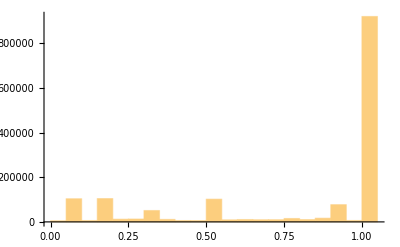

```mathematica
Histogram[Flatten[id]]
```